# Spatial probability of binding

We assume an energy landscape for kinesin (where l is length, and l0 is the rest length)

```mathematica
u=Piecewise[{{0,l<l0},{k (l-l0)^2/2,l≥l0}}]
```

Piecewise[{{0, l<l0}, {1/2 k (l-l0)^2, l≥l0}, {0, True}}]

Which, given our parameters, looks like this

```mathematica
params={kBT->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"],"Piconewtons"*"Micrometers"]],k->320,l0->.080,kon0->5}
```

{kBT→0.00414195,k→320,l0→0.08,kon0→5}

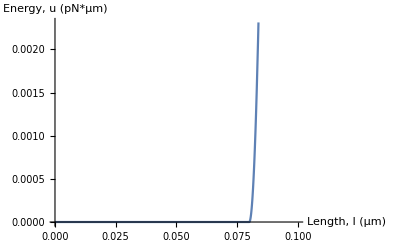

```mathematica
Plot[u/.params,{l,0,.1},AxesLabel->{"Length, l (μm)","Energy, u (pN*μm)"}]
```

We find the probability of kinesin being any length using this energy landscape by finding

```mathematica
p=1/z Exp[-u/kBT]
```

(ⅇ^(-Piecewise[{{0, l<l0}, {1/2 k (l-l0)^2, l≥l0}, {0, True}}]/kBT))/z

We find the partition function z by integrating  (with assumptions)

```mathematica
assump={kBT>0,k>0,l0>0,MTdist≥0}
```

{kBT>0,k>0,l0>0,MTdist≥0}

```mathematica
intvalue=Integrate[p,{l,0,Infinity},Assumptions->assump]
```

(2 l0+√(kBT/k) √(2 π))/(2 z)

and setting equal to 1

```mathematica
zsol=Solve[intvalue==1,z]
```

{{z→1/2 (2 l0+√(kBT/k) √(2 π))}}

And we arrive at a probability of kinesin being a certain length of

```mathematica
psol=p/.zsol//First
```

(2 ⅇ^(-Piecewise[{{0, l<l0}, {1/2 k (l-l0)^2, l≥l0}, {0, True}}]/kBT))/(2 l0+√(kBT/k) √(2 π))

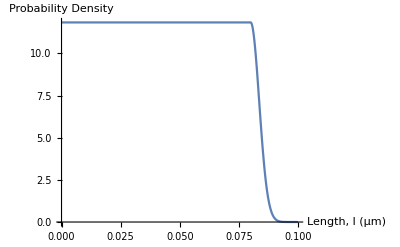

```mathematica
Plot[psol/.params,{l,0,.1},PlotRange->All,AxesLabel->{"Length, l (μm)","Probability Density"}]
```

This is uniform from 0 to l0, with a gaussian for l>l0 which has standard deviation Sqrt[kBT/k]

```mathematica
Refine[psol,l>l0]
```

(2 ⅇ^(-(k (l-l0)^2)/(2 kBT)))/(2 l0+√(kBT/k) √(2 π))

```mathematica
PDF[NormalDistribution[l0,σ],l]/.σ->Sqrt[kBT/k]
```

(ⅇ^(-(k (l-l0)^2)/(2 kBT)))/(√(kBT/k) √(2 π))

## On rate as a function of anchor-MT distance

This can be turned into an on rate by setting the on rate to 5 if l<l0

```mathematica
kon=kon0/Refine[(psol/.{l->0}),assump]psol
```

ⅇ^(-Piecewise[{{0, l<l0}, {1/2 k (l-l0)^2, l≥l0}, {0, True}}]/kBT) kon0

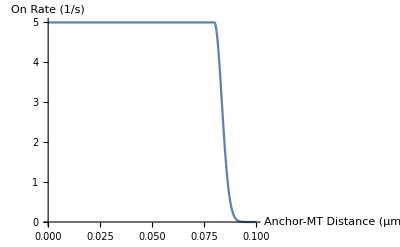

```mathematica
Plot[kon/.params,{l,0,.1},PlotRange->All,AxesLabel->{"Anchor-MT Distance (μm)","On Rate (1/s)"}]
```

We note that this binding rate is able to satisfy kon/koff=Exp[-ΔG/kBT], sometimes called detailed balance. The binding rate used in Bergman et al. was not able to, as kon was 0 for l>l0, while koff was positive in the same region (which would imply an infinite ΔG).

## Probability of binding at at a certain location on the MT

From this, we can derive the probability of binding at a certain spot on the microtubule, given the anchor location. From the anchor location and the MT location and vector, we find the perpendicular distance (already in the code). Then, from the perpendicular distance MTdist, we can find the shape of the probability of binding at a location x υm from the anchor

```mathematica
bindp=psol/.l->Sqrt[MTdist^2+x^2]
```

(2 ⅇ^(-Piecewise[{{0, √(MTdist^2+x^2)<l0}, {1/2 k (-l0+√(MTdist^2+x^2))^2, √(MTdist^2+x^2)≥l0}, {0, True}}]/kBT))/(2 l0+√(kBT/k) √(2 π))

However, these are not pdfs, as they do not integrate to 1.

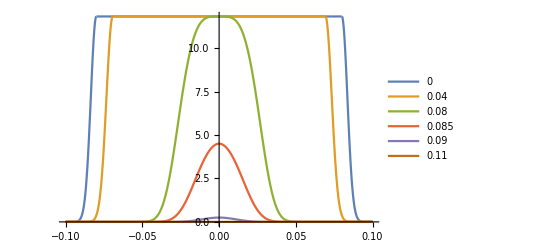

```mathematica
Plot[Table[bindp/.MTdist->i,{i,{0,.04,.08,.085,.09,.110}}]/.params//Evaluate,{x,-.1,.1},PlotRange->All,PlotLegends->{0,.04,.08,.085,.09,.110}]
```

Unfortunately, the normalization doesn’t seem to have a closed for solution

```mathematica
Integrate[bindp,{x,-Infinity,Infinity},Assumptions->assump]
```

Integrate[(2 ⅇ^(-Piecewise[{{0, √(MTdist^2+x^2)<l0}, {1/2 k (-l0+√(MTdist^2+x^2))^2, √(MTdist^2+x^2)≥l0}, {0, True}}]/kBT))/(2 l0+√(kBT/k) √(2 π)),{x,-∞,∞},Assumptions→{kBT>0,k>0,l0>0,MTdist≥0}]

We can normalize it by integrating numerically

```mathematica
ints=NIntegrate[Table[bindp/.MTdist->i,{i,{0,.04,.08,.085,.09,.110}}]/.params,{x,-Infinity,Infinity}]
```

{2.,1.76153,0.621811,0.150382,0.00649185,1.62142×10^-16}

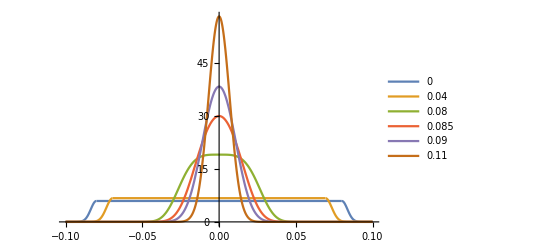

```mathematica
Plot[Table[bindp/.MTdist->i,{i,{0,.04,.08,.085,.09,.110}}]/ints/.params//Evaluate,{x,-.1,.1},PlotRange->All,PlotLegends->{0,.04,.08,.085,.09,.110}]
```

but this would be a real pain to implement in the C code. Furthermore, it would then require a way to draw random numbers from this distribution, which would also take some work. Because of this, we place the heads at the mean of the above distributions (right below the anchor)